```mathematica
f[er_]:=-5(er-5)^2+100
```

```mathematica
Function[er,-5 (er-5)^2+100]
```

Function[er,-5 (er-5)^2+100]

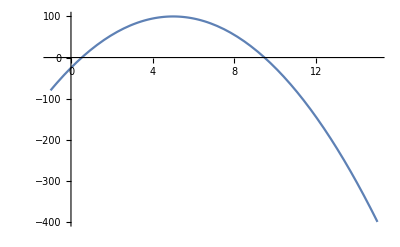

```mathematica
Plot[Function[er,-5 (er-5)^2+100][x],{x,-1,15}]
```

```mathematica
Function[er,-10 er (-10+er)]
```

Function[er,-10 er (-10+er)]

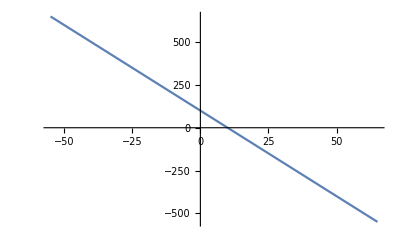

```mathematica
Plot[Function[er,-10 (-10+er)][x],{x,-55.,65.}]
```

```mathematica
Function[er,-10 er (er-10)]
```

Function[er,-10 er (er-10)]

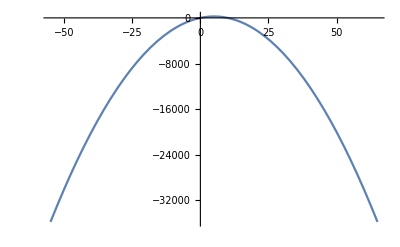

```mathematica
Plot[Function[er,-10 er (er-10)][x],{x,-55.,65.}]
```

```mathematica
Function[er,a (er-b)]
```

Function[x,a x (x-b)]

```mathematica
Function[er,a er(er-10)]
```

Function[x,a x (x-10)]

```mathematica
f[er]
```

a x (-b+x)

```mathematica
Manipulate[Plot[a er (-b+er),{er,-1,10}],{a,-10,10},{b,5,20}]
```

```mathematica
f[]
```

```mathematica
p[er_]:=-10*er(er-10)
```

```mathematica
Function[er,-10 er (er-10)]
```

Function[er,-10 er (er-10)]

```mathematica
Function[er,-10 er (er-10)]
```

Function[er,-10 er (er-10)]

```mathematica
u[]
```

```mathematica
f[x_]:=Piecewise[{{(x-r)^q],x>r},{0,x==r},{-L((x-r)^]),x<r}}]
```

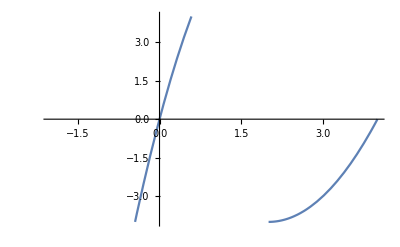

Manipulate::vsform: Manipulate argument {0,-10,10} does not have the correct form for a variable specification.

```mathematica
Function[x,Piecewise[{{1/(1+Exp[-10 (x-r)]),x>r},{0,x==r},{-1/(1+Exp[10 (x-r)]),x<r}}]]
```

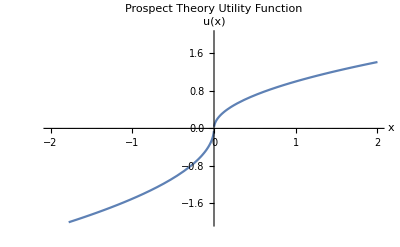

```mathematica
u[x_]:=Piecewise[{{x^(0.5),x>=0},{-1.5(-x)^0.5,x<0}}];

Plot[u[x],{x,-2,2},PlotRange->{-2,2},AxesLabel->{"x","u(x)"},PlotLabel->"Prospect Theory Utility Function",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/GoldenRatio]
```

```mathematica
u[x_]:=Piecewise[{{(x-r)^(0.5),x>=r},{-1.5 (-(x-r))^0.5,x<r}}];

Plot[u[x],{x,-2+r,2+r},PlotRange->{-2,2},AxesLabel->{"x-r","u(x-r)"},PlotLabel->"Prospect Theory Utility Function",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/GoldenRatio]
```

Plot::plln: Limiting value -2+r in {x,-2+r,2+r} is not a machine-sized real number.

Plot[u[x],{x,-2+r,2+r},PlotRange→{-2,2},AxesLabel→{x-r,u(x-r)},PlotLabel→Prospect Theory Utility Function,GridLines→{None,{0}},GridLinesStyle→Directive[Gray,Dashed],AspectRatio→1/GoldenRatio]

```mathematica
u[x_,r_]:=Piecewise[{{(x-r)^(0.5),x>=r},{-1.5(-(x-r))^(0.5),x<r}}]

Plot[u[x,r],{x,-1,3},{r,-1,3},PlotRange->{-2,2},AxesLabel->{"x","u(x)"},PlotLabel->"Prospect Theory Utility Function",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/GoldenRatio]
```

Plot::nonopt: Options expected (instead of {r,-1,3}) beyond position 2 in Plot[u[x,r],{x,-1,3},{r,-1,3},PlotRange→{-2,2},AxesLabel→{x,u(x)},PlotLabel→Prospect Theory Utility Function,GridLines→{None,{0}},GridLinesStyle→Directive[Gray,Dashed],AspectRatio→1/GoldenRatio]. An option must be a rule or a list of rules.

Plot[u[x,r],{x,-1,3},{r,-1,3},PlotRange→{-2,2},AxesLabel→{x,u(x)},PlotLabel→Prospect Theory Utility Function,GridLines→{None,{0}},GridLinesStyle→Directive[Gray,Dashed],AspectRatio→1/GoldenRatio]

```mathematica
u[x_,r_]:=Piecewise[{{(x-r)^0.5-(r^0.5),x>=r},{-1.5*(-(x-r))^0.5+1.5*(r^0.5),x<r}}]
```

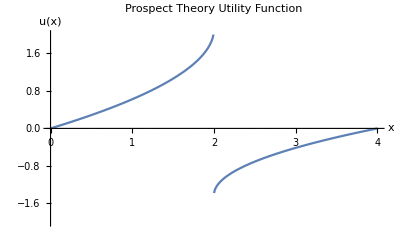

```mathematica
Plot[u[x,2],{x,0,4},PlotRange->{-2,2},AxesLabel->{"x","u(x)"},PlotLabel->"Prospect Theory Utility Function",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/GoldenRatio]
```

```mathematica
0^0.5
```

0.

```mathematica
Clear[pr]; (*fjern definitionen af pr*)
```

```mathematica
(*Indtast eksogene værdier*)pr=100; (*planlagt præstation*)
eps=10; (*usikkerhedsfaktor*)

(*Definer funktioner*)
f[er_]:=-5 (er-5)^2+100 (*effort-funktion*)
u[x_]:=Piecewise[{{Sqrt[x],x>=0},{-1.5 Sqrt[-x],x<0}}] (*utility-funktion*)

(*Definer problemfunktion*)
prob[er_]:=0.5 u[f[er]+eps-pr]+0.5 u[f[er]-eps-pr]

(*Find løsning numerisk*)
sol=NMaximize[{prob[er],0<=er<=10},er]

(*Udskriv løsning*)
Print["Optimal effort: ",er/. sol[[2]],", Utility: ",sol[[1]]]
```

{-0.790569,{er→5.}}

Optimal effort: 5., Utility: -0.790569

```mathematica
u[x_]:=Piecewise[{{x^(0.5),x>=0},{-1.5(-x)^0.5,x<0}}];

Plot[u[x],{x,-2,2},PlotRange->{-2,2},AxesLabel->{"x","u(x)"},PlotLabel->"Prospect Theory Utility Function",GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Function[er,-5 (er-5)^2+100]
```

Function[er,-5 (er-5)^2+100]

```mathematica
Plot[Function[er,-5 (er-5)^2+100][x],{x,-1,15}]
```

-Graphics-

```mathematica
Clear[pr]; (*fjern definitionen af p_r*)

(*Indtast eksogene værdier*)eps=50; (*usikkerhedsfaktor*)

(*Definer funktioner*)
f[er_]:=-5 (er-5)^2+100 (*effort-funktion*)
u[x_]:=Piecewise[{{Sqrt[x],x>=0},{-1.5 Sqrt[-x],x<0}}] (*utility-funktion*)

(*Definer problemfunktion*)
prob[er_,pr_]:=0.5 u[f[er]+eps-pr]+0.5 u[f[er]-eps-pr]

(*Find løsning numerisk*)
sol=NMaximize[{prob[er,pr],0<=er<=10,0<=pr<=100},{er,pr}]

(*Udskriv løsning*)
Print["Optimal effort: ",er/. sol[[2]],", Optimal performance: ",pr/. sol[[2]],", Utility: ",sol[[1]]]

(*Plot løsning*)
Plot3D[prob[er,pr],{er,0,10},{pr,0,100},AxesLabel->{"er","pr","Utility"},PlotLabel->"Total Utility",PlotRange->All,MeshFunctions->{#3&},Mesh->{{sol[[1]]}},MeshStyle->{Thick,Red}]
```

{9.65926,{er→5.,pr→0.}}

Optimal effort: 5., Optimal performance: 0., Utility: 9.65926

-Graphics3D-

```mathematica
Plot3D[prob[er,pr],{er,0,10},{pr,0,100},Mesh->All,MeshFunctions->Automatic,AxesLabel->{"er","pr","Utility"},PlotLabel->"Total Utility",PlotRange->All,MeshFunctions->{#3&},Mesh->{{sol⟦1⟧}},MeshStyle->{Thick,Red}]
```

-Graphics3D-

```mathematica
Plot3D[prob[er,pr],{er,0,10},{pr,0,100},Mesh->None,AxesLabel->{"er","pr","Utility"},PlotLabel->"Total Utility",PlotRange->All,MeshFunctions->{#3&},Mesh->{{sol⟦1⟧}},MeshStyle->{Thick,Red}]
```

-Graphics3D-

```mathematica
Clear[pr];
Clear[er];
```

```mathematica
(*Indtast eksogene værdier pr=80; (*planlagt præstation*)
eps=10; (*usikkerhedsfaktor*)*)

(*Definer funktioner*)
pr[er_]:=-5 (er-5)^2+100 (*performance-funktion*)
f[ea_]:=-5 (ea-5)^2+100 (*effort-funktion*)

Solve[pr[er]==80,er]
```

{{er→3},{er→7}}

```mathematica
er=3
```

3

```mathematica
(*Indtast eksogene værdier*) 
eps=10; (*usikkerhedsfaktor*)
```

```mathematica
u[x_]:=Piecewise[{{Sqrt[x],x>=0},{-1.5 Sqrt[-x],x<0}}] (*utility-funktion*)

(*Definer problemfunktion*)
prob[ea_]:=0.5 u[pr[er]+f[ea]+eps-80]+0.5 u[pr[er]+f[ea]-eps-80](*pr is 80*)

(*Find løsning numerisk*)
sol=NMaximize[{prob[er],0<=ea<=10},ea]

(*Udskriv løsning*)
Print["Optimal effort: ",ea/. sol[[2]],", Utility: ",sol[[1]]]
```

{8.92672,{ea→0.}}

Optimal effort: 0., Utility: 8.92672

```mathematica
Clear[pr];
Clear[eps];
Clear[er];
```

```mathematica
(*Indtast eksogene værdier*)pr=pr; (*planlagt præstation*)
eps=eps; (*usikkerhedsfaktor*)

(*Definer funktioner*)
f[er_]:=-a(er-b)^2+c (*effort-funktion*)
u[x_]:=Piecewise[{{Sqrt[x],x>=0},{-L Sqrt[-x],x<0}}] (*utility-funktion*)

(*Definer problemfunktion*)
prob[er_]:=p1 u[f[er]+eps-pr]+(1-p1) u[f[er]-eps-pr]

(*Find løsning numerisk*)
sol=NMaximize[{prob[er],0<=er},er]

(*Udskriv løsning*)
Print["Optimal effort: ",er/. sol[[2]],", Utility: ",sol[[1]]]
```

NMaximize::nnum: The function value -((1-p1) (Piecewise[{{√(Times[«3»]+c+Times[«2»]+Times[«2»]), Times[«3»]+c+Times[«2»]+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+Times[«2»]+Times[«2»]<0}, {0, True}}]))-p1 (Piecewise[{{√(Times[«3»]+c+eps+Times[«2»]), Times[«3»]+c+eps+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+eps+Times[«2»]<0}, {0, True}}]) is not a number at {er} = {0.0914636}.

NMaximize[{(1-p1) (Piecewise[{{√(c-eps-a (-b+er)^2-pr), c-eps-a (-b+er)^2-pr≥0}, {-L √(-c+eps+a (-b+er)^2+pr), c-eps-a (-b+er)^2-pr<0}, {0, True}}])+p1 (Piecewise[{{√(c+eps-a (-b+er)^2-pr), c+eps-a (-b+er)^2-pr≥0}, {-L √(-c-eps+a (-b+er)^2+pr), c+eps-a (-b+er)^2-pr<0}, {0, True}}]),0≤er},er]

NMaximize::nnum: The function value -((1-p1) (Piecewise[{{√(Times[«3»]+c+Times[«2»]+Times[«2»]), Times[«3»]+c+Times[«2»]+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+Times[«2»]+Times[«2»]<0}, {0, True}}]))-p1 (Piecewise[{{√(Times[«3»]+c+eps+Times[«2»]), Times[«3»]+c+eps+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+eps+Times[«2»]<0}, {0, True}}]) is not a number at {er} = {0.0914636}.

ReplaceAll::reps: {er} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value -((1-p1) (Piecewise[{{√(Times[«3»]+c+Times[«2»]+Times[«2»]), Times[«3»]+c+Times[«2»]+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+Times[«2»]+Times[«2»]<0}, {0, True}}]))-p1 (Piecewise[{{√(Times[«3»]+c+eps+Times[«2»]), Times[«3»]+c+eps+Times[«2»]≥0}, {-L √Plus[«4»], Times[«3»]+c+eps+Times[«2»]<0}, {0, True}}]) is not a number at {er} = {0.0914636}.

Optimal effort: er/.er, Utility: {(1-p1) (Piecewise[{{√(c-eps-a (-b+er)^2-pr), c-eps-a (-b+er)^2-pr≥0}, {-L √(-c+eps+a (-b+er)^2+pr), c-eps-a (-b+er)^2-pr<0}, {0, True}}])+p1 (Piecewise[{{√(c+eps-a (-b+er)^2-pr), c+eps-a (-b+er)^2-pr≥0}, {-L √(-c-eps+a (-b+er)^2+pr), c+eps-a (-b+er)^2-pr<0}, {0, True}}]),0≤er}

{{x→b}}

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,er]